## Setting

```mathematica
ClearAll[Evaluate[$Context<>"*"]]
Needs["ErrorBarPlots`"];

plotparameters=Evaluate[{Frame->True,BaseStyle->{FontSize->16,FontFamily->"Arial",FontColor->Black},LabelStyle->{FontSize->22,FontFamily->"Arial",FontColor->Black}},Axes -> {False, False}, Method->{"OptimizePlotMarkers"->False},FrameStyle->Thickness[0.003]];

SetOptions[Plot,plotparameters];
SetOptions[ListLinePlot,plotparameters];
SetOptions[ListPlot,plotparameters];
SetOptions[ErrorListPlot,plotparameters];
SetOptions[ListContourPlot,plotparameters];
SetOptions[ListLogLogPlot,plotparameters];
SetOptions[ListLogPlot,plotparameters];
SetOptions[Style,SingleLetterItalics->False];
verticalSize=250;
SetDirectory["~/Works/adaptive_potential/distribution/convolution/p2/"];
```

## Parameters and functions

```mathematica
A=1;
σ0=1;
L=8;
d=0.4;
density=0.7;
dis=0.01;
τ=0.5;
β=1;
σ1=0.5;
σ2=1.5;
τ1=0.25;
τ2=0.25;
ρ10=1;
ρ20=0.5654856738275738;
ρ1[z_]:=ρ10 Exp[-β A σ0 z];
ρ2[z_]:=ρ20 Exp[(1/2 β A τ z-σ0/τ)^2-σ0^2/τ^2];
ρ3[z_]:=ρ30 (Exp[(1/2 β A τ1 z-σ1/τ1)^2-σ1^2/τ1^2]+Exp[(1/2 β A τ2 z-σ2/τ2)^2-σ2^2/τ2^2]);
p2[σ_]:=Exp[-(σ-σ0)^2/τ^2]
p3[σ_]:=Exp[-(σ-σ1)^2/τ1^2]+Exp[-(σ-σ2)^2/τ2^2]
ϕ[r_,σ_]:=A*σ*r
B21[σ_,c_]:=c*σ^3
B22[σ_,c_]:=c*d^3*(Exp[β*Abs[σ]]-1)
dis=0.01;
tol = 0.001;
den = 0;
```

## ρ_2(r,σ) with second virial expansion coefficient B_2

### initial condition (ideal gas)

```mathematica
(*Normalization: ∫_0^L ρ(z)dz=L/d^3*)
q=0.7977987101238614;
ρin=1/10;
While[Abs[den-density]>tol,
Do[
ρsideal[σ,z]=ρ/.FindRoot[ρ==q*Exp[-β*((σ-σ0)^2/τ^2+A*σ*z)],{ρ,ρin}];
,{z,0,L,dis},{σ,-4,5,dis}];
data1 =Table[ρsideal[σ,z],{σ,-4,5,dis},{z,0,L,dis}];
den = Total[Total[data1[[All,All]]]]*dis*dis;
q = q * density/ den;
Print[den];
]
```

0.855833

0.7

### B_2(σ) = c̃ d^3[exp(βσ)-1]

```mathematica
c=-5;
(*Normalization: ∫_0^L ρ(z)dz=L/d^3*)
q=0.7977987101238614;
den = 0;
While[Abs[den - density]>tol,
Do[
ρs1[σ,z]=q*Exp[-β*(2*B22[σ,c]*Total[data1[[All,Round[z*100+1]]]]*dis+(σ-σ0)^2/τ^2+A*σ*z)];
,{σ,-4,5,dis},{z,0,L,dis}];
data2 =Table[ρs1[σ,z],{σ,-4,5,dis},{z,0,L,dis}];
(*Export["rho_sig_z_b21_c05.txt",data2];*)
Do[
Nprofile[σ]=N[Total[data2[[σ,All]]]*dis]
,{σ,1,Length[data2[[All,1]]],1}];

Do[
ρprofile[z]= N[Total[data2[[All,z]]]*dis];
,{z,1,Length[data2[[1,All]]],1}];

datarhozb21c05=Table[{z*dis,ρprofile[z]},{z,1,Length[data2[[1,All]]],1}];
dataNsigb21c05=Table[{σ*dis-4,Nprofile[σ]},{σ,1,Length[data2[[All,1]]],1}];
den=Total[datarhozb21c05[[All,2]]]*dis;
q = q *density/ den;
Print[den];
]
```

1.19729

0.7

```mathematica
Do[
temp=0;
Do[
temp=temp+data2[[σ,z]]*((σ-1)*dis-4);
,{σ,1,Length[data2[[All,1]]],1}];
sigzprofile[z] =temp  * dis;
,{z,1,Length[data2[[1,All]]],1}] 
sigztable = Table[{z*dis,sigzprofile[z]/ρprofile[z]},{z,1,Length[data2[[1,All]]]}];
Export["sig_z_b22_c-5.txt",sigztable];
data2[[601,1]]
```

0.0908993

```mathematica
Export["rho_z_b22_c-5.txt",Flatten/@datarhozb21c05,"Table"];
Export["N_sig_b22_c-5.txt",Flatten/@dataNsigb21c05,"Table"];
```

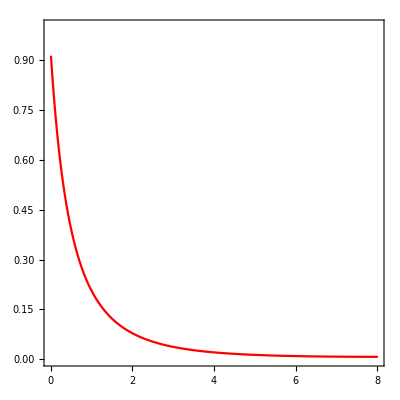

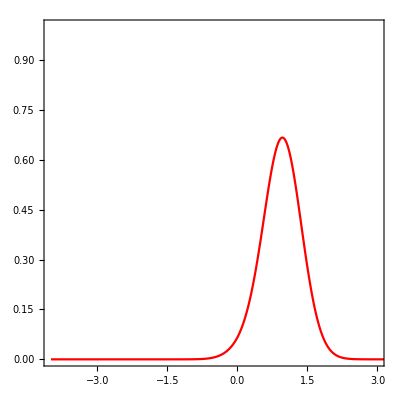

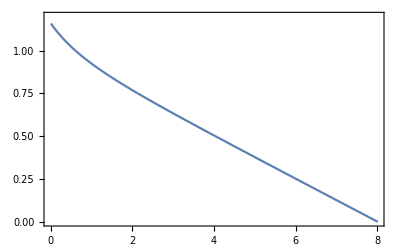

```mathematica
plotb21c05=ListLinePlot[Table[{z*dis,ρprofile[z]},{z,1,Length[data2[[1,All]]],1}],PlotStyle->Red,PlotRange->{{0,L},{0,1}},AspectRatio->1]
plotNb21c05=ListLinePlot[Table[{σ*dis-4,Nprofile[σ]},{σ,1,Length[data2[[All,1]]],1}],PlotStyle->Red,PlotRange->{{-4,3},{0,1}},AspectRatio->1]
plotsigz = ListLinePlot[sigztable,PlotRange-> {{0,L},{0,1.2}}]
```